```mathematica
D2[n_,k_]:=D2[n,k]=Sum[D2[Floor[n/j],k-1],{j,2,n}];D2[n_,0]:=D2[n,0]=1
DD[n_,k_]:=DD[n,k] = Sum[DD[Floor[n/j],k-1],{j,1,n}];DD[n_,0]:=DD[n,0] =1
T1:= T1=Table[ Residue[ ( Zeta[s])^k x^s s^(-1),{s,1}],{k,1,15}]
T2:= T2=Table[ Residue[ ( Zeta[s]-1)^k x^s s^(-1),{s,1}],{k,1,15}]
T2cal:= T2cal=Table[T2[[k]]/. x->1,{k,1,15}]
Ap[n_,k_] := (-1)^(k)(1-Gamma[k,-Log[n]]/Gamma[k])
```

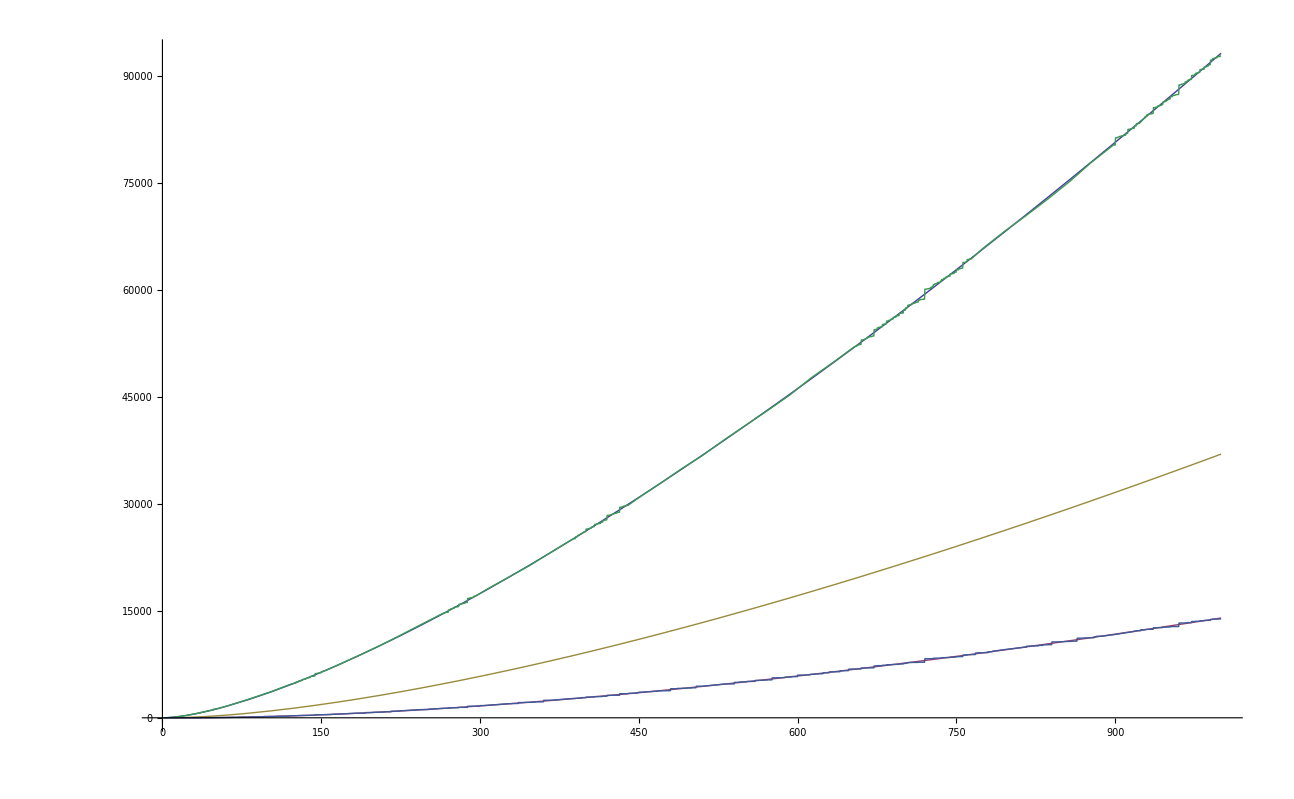

```mathematica
Plot[ {(T1[[tt=4]]/.x->n),(T2[[tt]]/.x->n)-T2cal[[tt]], Ap[n,tt], DD[Floor[n],tt], D2[Floor[n],tt] },{n,1,1000}]
```

```mathematica
T1[[2]]
```

-x+2 EulerGamma x+x Log[x]

```mathematica
T2[[2]]
```

-3 x+2 EulerGamma x+x Log[x]

```mathematica
T2a[n_] := Sum[ (-1)^(k+1)/k((T2[[k]]/.x->n)-T2cal[[k]]),{k,1,15}]
```

```mathematica
N[T2a[100]]
```

30.6209

```mathematica
N[T2a[100]]-N[LogIntegral[100]]
```

0.494743

```mathematica
N[Log[Log[100]]]
```

1.52718

```mathematica
N[EulerGamma]
```

0.577216

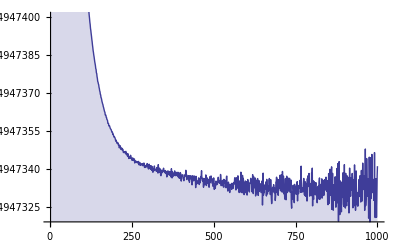

```mathematica
DiscretePlot[ T2a[n]-LogIntegral[n],{n,2,1000}]
```

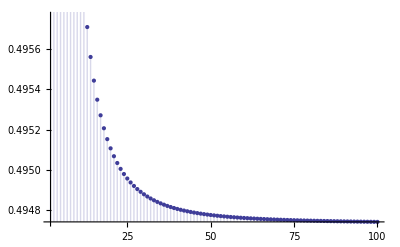

```mathematica
DiscretePlot[ T2a[n]-LogIntegral[n],{n,2,100}]
```

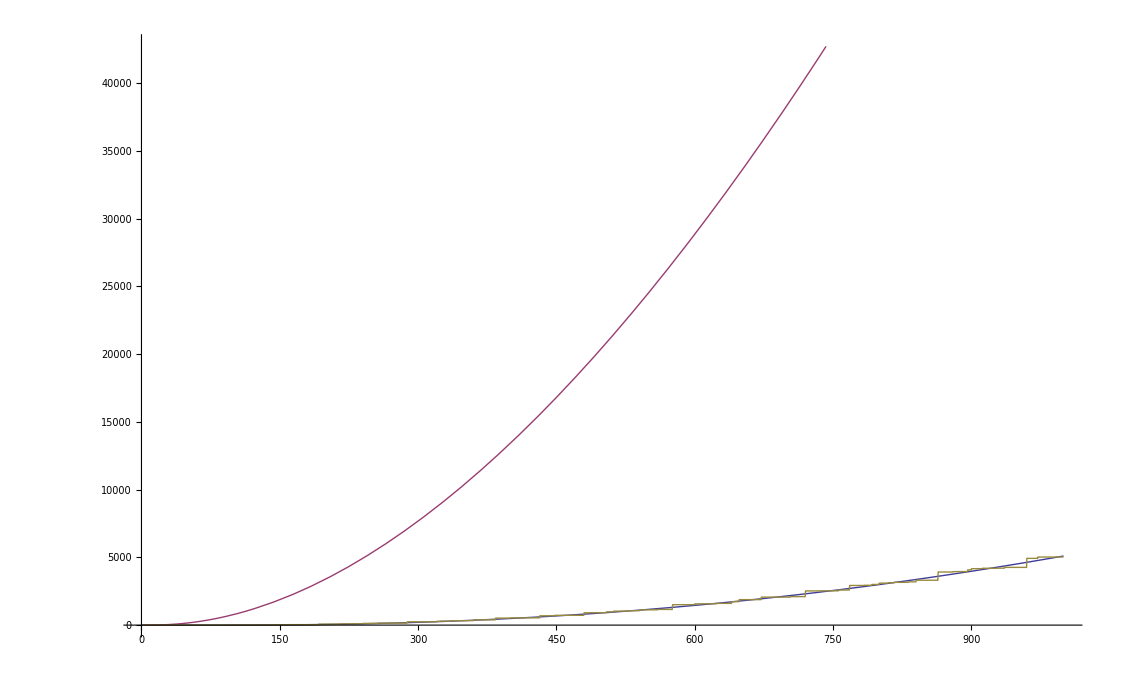

```mathematica
Plot[ {(T2[[tt=6]]/.x->n), Ap[n,tt], D2[Floor[n],tt] },{n,1,1000}]
```

```mathematica
T2[[2]]
```

-3 x+2 EulerGamma x+x Log[x]

```mathematica
T1[[2]]
```

-x+2 EulerGamma x+x Log[x]

```mathematica
Test[j_]:=Sum[ T1[[k]] Binomial[j,j-k] (-1)^(j-k),{k,1,j}]
```

```mathematica
Expand[Test[4]]
```

-15 x+28 EulerGamma x-18 EulerGamma^2 x+4 EulerGamma^3 x+11 x Log[x]-16 EulerGamma x Log[x]+6 EulerGamma^2 x Log[x]-5/2 x Log[x]^2+2 EulerGamma x Log[x]^2+1/6 x Log[x]^3+16 x StieltjesGamma[1]-12 EulerGamma x StieltjesGamma[1]-4 x Log[x] StieltjesGamma[1]+2 x StieltjesGamma[2]

```mathematica
T2[[6]]-Test[6]
```

```mathematica
T2[[4]] /. x->1
```

1/6 (-90+168 EulerGamma-108 EulerGamma^2+24 EulerGamma^3+96 StieltjesGamma[1]-72 EulerGamma StieltjesGamma[1]+12 StieltjesGamma[2])

```mathematica
T2cal[[3]]
```

1/2 (14-18 EulerGamma+6 EulerGamma^2-6 StieltjesGamma[1])